## Ralston Method

```mathematica
FancyRalstonStep[f_,h_][{t0_,y0_}]:= Module[
{k1,k2,k3,k4,z1,z2,z3,w},
k1=f[t0,y0];
z1 = y0+1/2 * k1*h; 
k2 = f[t0+1/2 h, z1];
z2= y0 + 3/4*k2*h;
k3=f[t0+3/4 h, z2];
z3=y0 + h*(2/9 k1+1/3 k2 + 4/9 k3);
k4=f[t0+h,z3];
w=y0+h*(7/24 k1 + 1/4 k2 + 1/3 k3 + 1/8 k4);
{t0+h, w,z3}
]
```

Generate a “synthetic” ODE with a known solution

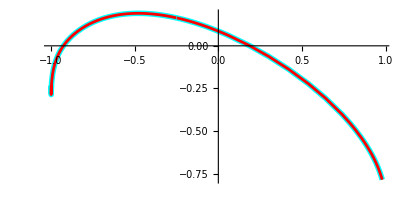

```mathematica
Clear[SynSol,ySol, f,t,y,g]
SynSol[t_]:= {Cos[t+Sin[t]], Sin[t] - Cos[Sin[t]-ArcTan[Cos[ t+ 2]+t]]}
g[t_,{y1_,y2_}]:={3.2 (y2+Sin[2 t]^2)Cos[t+y1], 2.3 t + Sin[t + y2]};
ff[t_]= Simplify[ SynSol'[t]-g[t,SynSol[t]]];
f[t_,y_]:=g[t,y]+ff[t]
t0=0.1; y0=SynSol[t0];
TMax=3.4;
ySol=NDSolveValue[ {y'[t]==f[t,y[t]],y[t0]==y0},y,{t,t0, t0+TMax}];
ParametricPlot[{ySol[t],SynSol[t]},{t, t0, t0+TMax},
PlotStyle->{{Cyan, Thickness[0.01]},{Red,Thickness[0.005]}}]
```

Lets look at the single steps we generate from the FancyRalston procedure as a function of h.  One of the methods is much more accurate than the other! One is order 3 and the other is order 2.

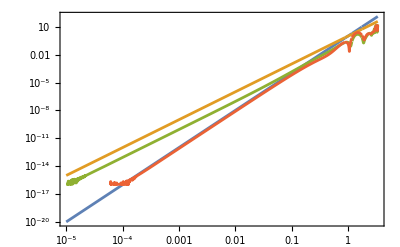

```mathematica
LogLogPlot[ {h^4,h^3,
Norm[FancyRalstonStep[f,h][{t0,y0}]⟦2⟧-SynSol[t0+h]],
Norm[FancyRalstonStep[f,h][{t0,y0}]⟦3⟧-SynSol[t0+h]]
},{h,10^-5,TMax},
GridLines->Automatic,Frame->True]
```

We know what it does!  We need to work out the two pieces of information are useful.
I know when h is small that 
	||y[t0+h]-z||≈C_1 h^4 and ||y[t0+h]-w||≈C_2 h^3
so 
	||w-z||=||w-y[t0+h]+y[t0+h]-z||≤||w-y[t0+h]||+||y[t0+h]-z||
and
	||w-z||≈C_1 h^4+C_2 h^3≈C_2 h^3.
In words, the computable difference between the two predictions scales like h^3. Perhaps more usefully
	||w-y[t0+h]||=||w-y[t0+h]+y[t0+h]-z||≤||w-y[t0+h]||+||y[t0+h]-z||

```mathematica
SolPic=ParametricPlot[SynSol[t],{t, t0, t0+TMax},
PlotStyle->{Cyan, Thickness[0.01]}];
n=4
Data=NestList[ FancyRalstonStep[f,h],{t0,y0},n];
Dimensions[Data]
```

4

{5}

```mathematica
Manipulate[
h=TMax/n;
Data=NestList[ FancyRalstonStep[f,h],{t0,y0},n];
Show[SolPic,Graphics[Point[Data⟦All,3⟧]]],
{{n,6},2,20,1}]
```

Part::partw: Part 3 of {0.1,{0.9801,-0.78507}} does not exist.

Our aim is to have an algorithm pick the step size to ensure that the data matches the solution to some reasonable accuracy.   The first thing to do is understand the behavior of a single step of our algorithm. Why does it look like this? What function would match the “straight” line section?

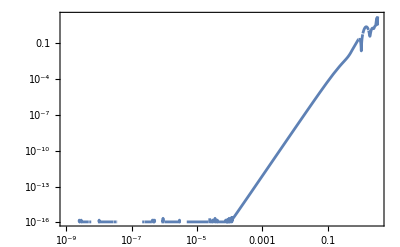

```mathematica
LogLogPlot[ Norm[RalstonStep[f,h][{t0,y0}]⟦2⟧-SynSol[t0+h]],{h,10^-9,TMax},
GridLines->Automatic,Frame->True]
```

It looks like a straight line because the numbers (the fancy word is coefficients) in the Ralston code are chosen to match the Taylor series of RalstonStep[f,h][{t0,y0}] and y[t0+h] for the first few powers of h. Note, y[t] is the solution of y'=f[t,y] and the matching needs to happen for every smooth function f.

```mathematica
Clear[h]
Series[RalstonStep[f,h][{t0,y0}],{h,0,2}]
Series[SynSol[t0+h],{h,0,2}]
```

{0.1+h+O[h]^3,{0.9801-0.39602 h-1.94051 h^2+O[h]^3,-0.78507+1.40371 h+0.163885 h^2+O[h]^3}}

{0.9801-0.39602 h-1.94051 h^2+O[h]^3,-0.78507+1.40371 h+0.163885 h^2+O[h]^3}

The order of a method is how far up the series match! The Ralston method has order 3.

```mathematica
Clear[h]
Series[RalstonStep[f,h][{t0,y0}],{h,0,4}]⟦2⟧
Series[SynSol[t0+h],{h,0,4}]
```

{0.9801-0.39602 h-1.94051 h^2+0.393218 h^3+1.74207 h^4+O[h]^5,-0.78507+1.40371 h+0.163885 h^2-0.574085 h^3-0.177113 h^4+O[h]^5}

{0.9801-0.39602 h-1.94051 h^2+0.393218 h^3+0.949386 h^4+O[h]^5,-0.78507+1.40371 h+0.163885 h^2-0.574085 h^3-0.179841 h^4+O[h]^5}